# Kapitola 7 - Pokrytí dat jednoduchou RBF sítí Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují dva dobře oddělené shluky dat, každý shluk reprezentuje jednu třídu.
Vygenerujeme tyto dva shluky dat.

```mathematica
values=50;
cluster1 =RandomReal[{-2,1},{values,2}];
cluster2=RandomReal[ {9,12},{values,2}];
inData = Join[cluster1,cluster2];
outcluster1=ConstantArray[{1,0},{values}];
outcluster2 = ConstantArray[{0,1},{values}];
outData= Join[outcluster1,outcluster2];
```

Takto vypadají naše vynerovaná vstupní data. Data můžeme chápat jako seznam bodů, určených svými {x,y} souřadnicemi.

```mathematica
inData
```

{{0.84474,-1.26105},{-1.68158,0.620504},{-1.40559,-1.56908},{-1.92738,-1.73595},{-0.262923,0.601228},{-0.403241,-1.43762},{-0.272428,-0.862862},{-0.774567,-1.58912},{-0.994217,0.700393},{-0.839124,0.792947},{-1.70516,0.162454},{-0.365553,-0.443195},{0.664203,-1.1118},{0.658716,0.288844},{-0.542672,-1.96493},{-0.371799,0.997649},{-0.173609,0.0231793},{0.168987,-1.777},{-1.84537,0.410821},{-0.585716,-0.487025},{-1.05308,-1.12228},{-1.51536,-1.89816},{0.976593,-0.660471},{0.716638,-1.49899},{0.736218,0.774349},{0.399329,0.690209},{-1.25395,0.0149111},{0.320069,-1.44175},{0.302049,0.183046},{-0.559208,-1.64487},{-0.0612953,-1.65726},{-1.28059,-0.954882},{-1.56199,-1.0375},{0.258526,0.467939},{0.539771,-1.50391},{0.162114,-1.5076},{0.698842,-1.0035},{-0.0231159,-0.552545},{0.817676,0.452706},{-0.924767,-0.736128},{0.778801,-1.20137},{0.391061,-1.51332},{-0.868072,-1.23047},{0.0843474,-1.19116},{-0.683049,0.485621},{0.907787,0.229791},{-0.772713,0.244094},{0.847037,-1.74446},{-0.376412,-0.468705},{-1.29427,0.888617},{9.14843,11.9316},{10.1838,10.6849},{10.1421,9.55514},{11.6353,10.497},{10.9078,11.0833},{9.49335,10.9653},{10.5045,10.4814},{9.98509,11.6607},{10.2226,11.5904},{11.8209,9.84036},{9.86414,10.4481},{11.0954,9.42669},{9.813,11.7799},{11.2944,11.1238},{11.1963,9.3134},{10.9215,9.98594},{10.3413,9.79269},{10.4966,11.025},{9.9144,11.9714},{10.5709,11.7438},{9.36273,9.27191},{11.0129,10.0121},{10.3313,10.6785},{9.36098,11.5455},{11.6291,11.7785},{11.8751,11.5354},{9.98507,11.8037},{11.2374,10.983},{9.07325,10.9439},{10.5054,11.8736},{11.5234,9.69496},{9.32523,11.1459},{10.5992,9.4028},{11.0196,10.632},{11.5358,10.2817},{11.577,9.20801},{11.7937,10.4348},{9.39122,9.65015},{10.2004,9.89192},{11.8106,10.7719},{9.25092,10.9104},{11.3713,10.3085},{10.4651,10.893},{9.74415,11.3238},{11.2942,11.1727},{11.7182,11.8403},{11.998,11.4552},{11.7789,11.4763},{9.24245,10.0995},{11.1145,9.035}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat je reprezentována jinou barvou.

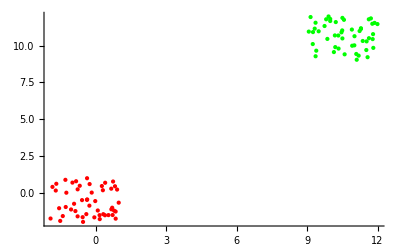

```mathematica
ListPlot[{cluster1,cluster2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1, OutputNonlinearity->Sigmoid,LinearPart->False,RandomInitialization->True]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 21, 22, 40, 15.911578}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-21 at 22:40. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

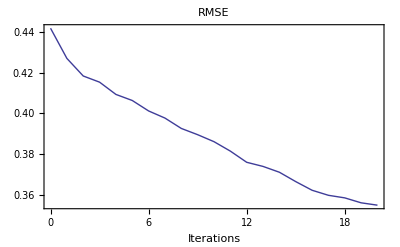

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Podívejme se jak naše síť klasifikuje data.

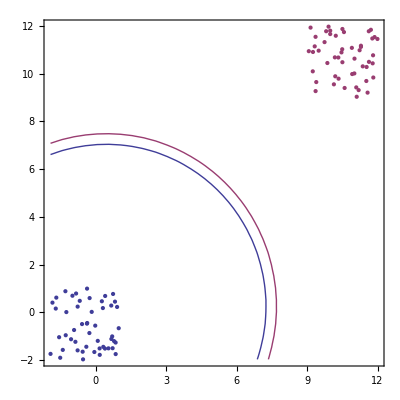

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronu

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Pro získání výstupu RBF neuronu je třeba upravit strukturu sítě. RBF neuron napojíme přímo na výstupní neuron s vahou 1. Na tomto výstupním neuronu uvidíme přímo výstup RBF neuronu. Následujísí obrázek zobrazuje síť před prováděnými úpravami.

Následující obrázek ukazuje síť po provedené úpravě. Síť má pouze jeden výstup protože máme pouze jeden RBF neuron.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[1],{0}];(*změna matice vah na výstupu*)
```

A zobrazíme výstup RBF neuronu.

```mathematica
gauss=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data pro lepší představu o jejich pokrytí.

```mathematica
cluster13d=cluster1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
cluster23d=cluster2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
gaussO=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All,PlotStyle->Opacity[0.5]];
data3d=ListPointPlot3D[{cluster13d,cluster23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gaussO,data3d]
```

-Graphics3D-

## Prohlášení

Tento text je vypracován jako součást bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.